```mathematica
El1[x_,t_] = E11*Cos[w*t]*Cos[k1*x]+E12*Cos[w*t]*Sin[k1*x]+
                         E13*Sin[w*t]*Cos[k1*x]+E14*Sin[w*t]*Sin[k1*x];

El2[x_,t_] = E21*Cos[w*t]*Cos[k2*x]+E22*Cos[w*t]*Sin[k2*x]+
                         E23*Sin[w*t]*Cos[k2*x]+E24*Sin[w*t]*Sin[k2*x];

Hf1[x_,t_] = H11*Cos[w*t]*Cos[k1*x]+H12*Cos[w*t]*Sin[k1*x]+
                         H13*Sin[w*t]*Cos[k1*x]+H14*Sin[w*t]*Sin[k1*x];

Hf2[x_,t_] = H21*Cos[w*t]*Cos[k2*x]+H22*Cos[w*t]*Sin[k2*x]+
                         H23*Sin[w*t]*Cos[k2*x]+H24*Sin[w*t]*Sin[k2*x];
```

```mathematica
Simplify[D[El1[x,t],t]-D[Hf1[x,t],x]]
```

0

```mathematica
H12 = E13;
H11 = -E14;
H14 = -E11;
H13 = E12;
k1 = w;
```

```mathematica
Simplify[eps*D[El2[x,t],t]-D[Hf2[x,t],x]]
```

0

```mathematica
k2   = w*Sqrt[eps];
H22 = E23*Sqrt[eps];
H21 = -E24*Sqrt[eps];
H24 = -E21*Sqrt[eps];
H23 = E22*Sqrt[eps];
```

```mathematica
Simplify[D[Hf2[x,t],t]-D[El2[x,t],x]]
```

0

```mathematica
Simplify[ El1[-1,t]-El2[1,t] ]
```

0

```mathematica
Simplify[ Hf1[-1,t]-Hf2[1,t] ]
```

0

```mathematica
eps = 4;
w = 2*Pi;
```

```mathematica
Simplify[ Hf1[0,t]-Hf2[0,t] ]
```

0

```mathematica
E14 = E24*Sqrt[eps];
E12 = E22*Sqrt[eps];
```

```mathematica
Simplify[ El1[0,t]-El2[0,t] ]
```

0

```mathematica
E11 = E21;
E13 = E23;
```

```mathematica
F[w_,eps_] = (Cos[w]-Cos[√eps w])^2+(-√eps Cos[w]+√eps Cos[√eps w])^2+(√eps Sin[w]+Sin[√eps w])^2+(Sin[w]+√eps Sin[√eps w])^2;
g[w_] = F[w,4]
```

(Cos[w]-Cos[2 w])^2+(-2 Cos[w]+2 Cos[2 w])^2+(2 Sin[w]+Sin[2 w])^2+(Sin[w]+2 Sin[2 w])^2

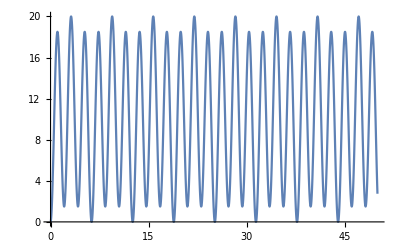

```mathematica
Plot[g[w],{w,0,50}]
```

```mathematica
FindRoot[g[w],{w,6}]
```

{w→6.28319}